```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sam\Documents\GitHub\RLUtilities\examples\10_speedcontrol

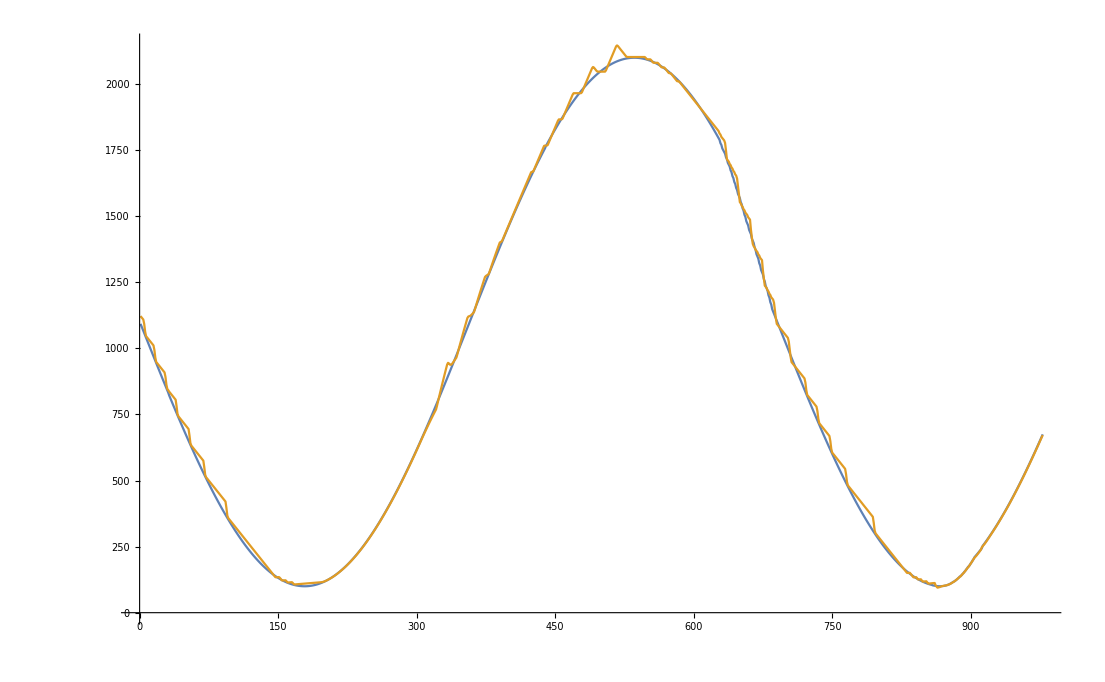

```mathematica
data = Import["speed_controller.txt", "CSV"];
ListLinePlot[Transpose[data[[25;;-1, 1;;2]]]]
```

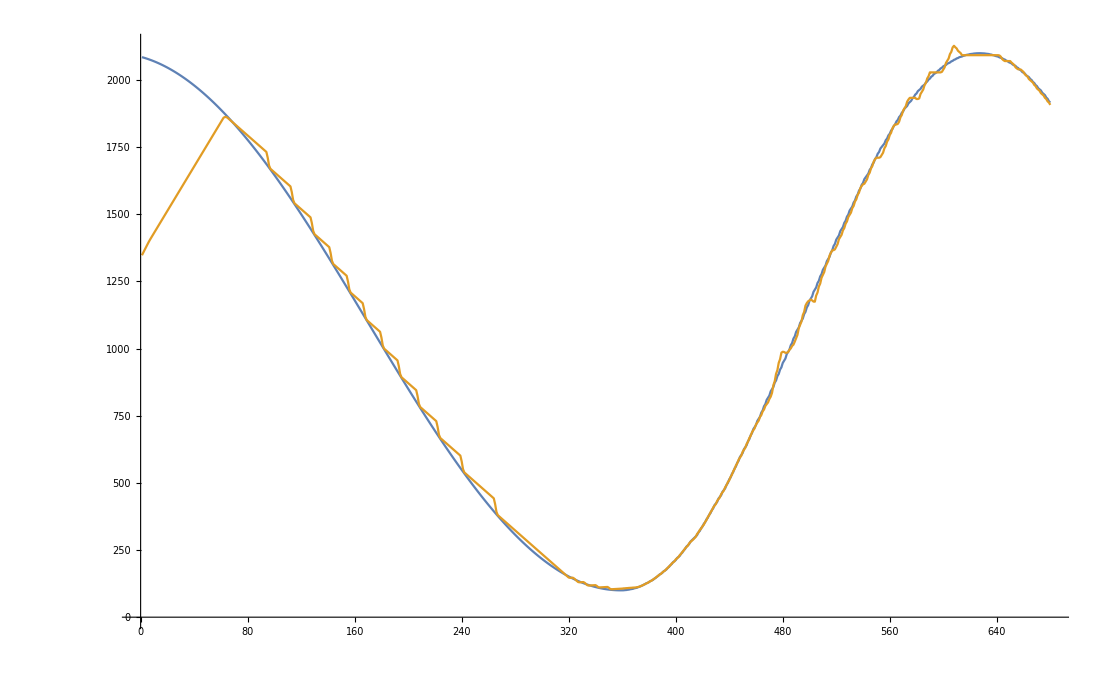

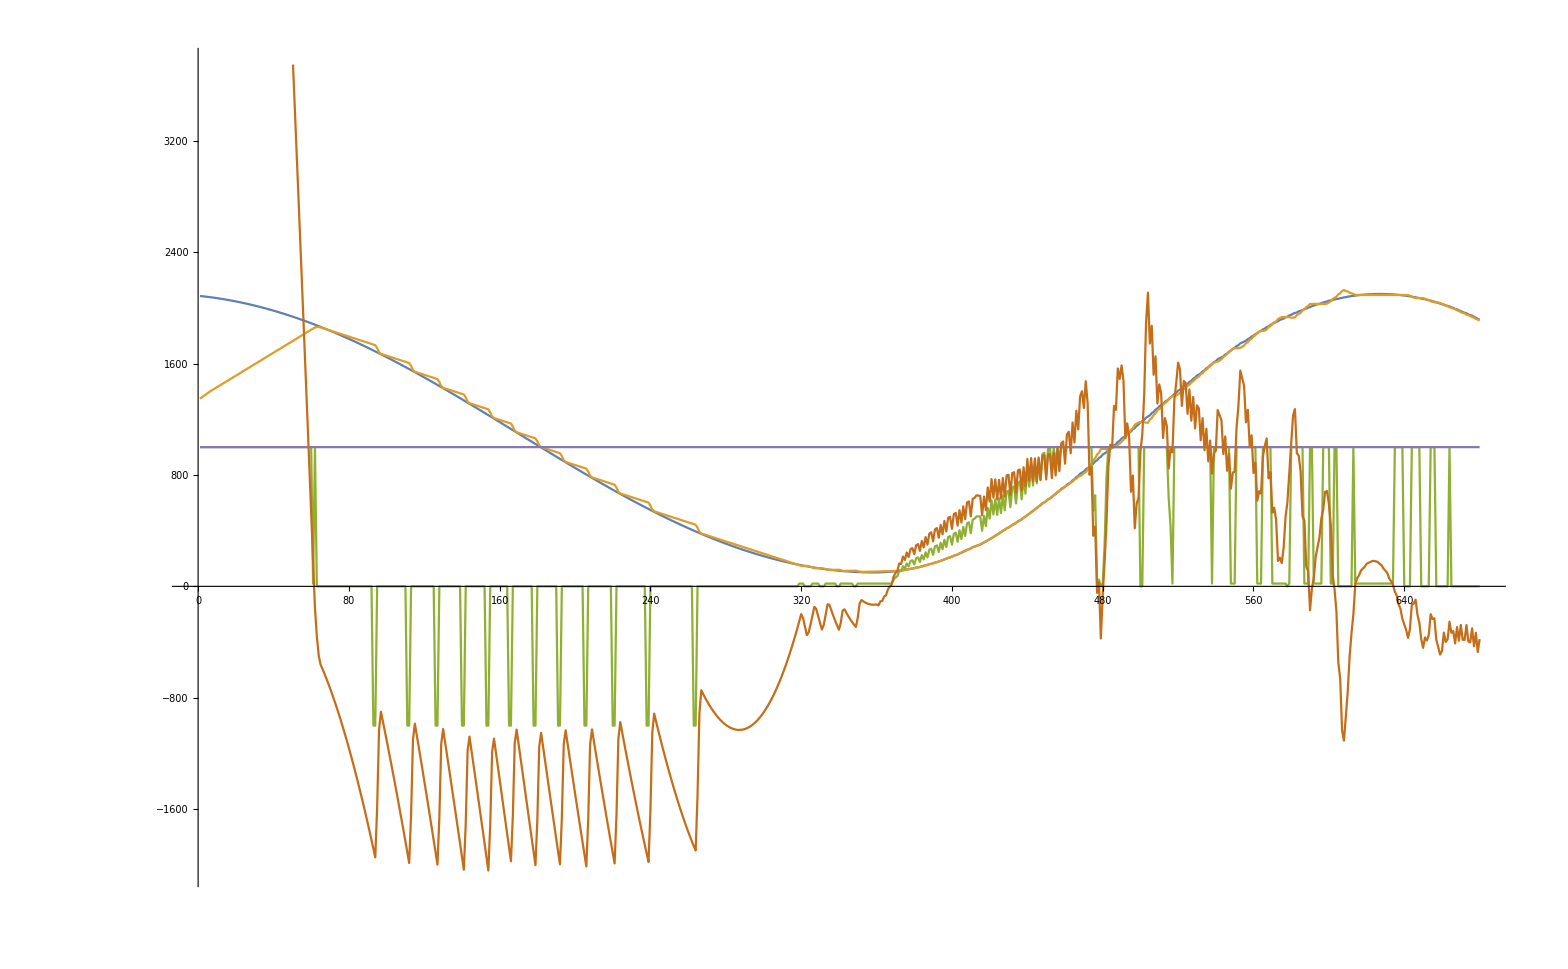

```mathematica
ListLinePlot[Transpose[# * {1, 1, 1000, 500, 10000, 1}& /@ data[[25;;-1]]]]
```